# Archetypal Quest

### Let’s start easy: Mean

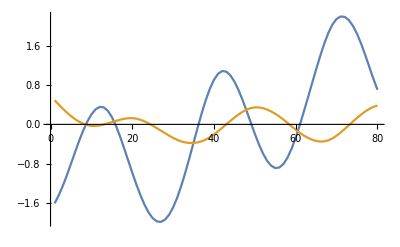

```mathematica
archetypalMeanYes=Table[Mean[Table[reducedOxyYes80[[x,y]],{x,30}]],{y,2}];
ListLinePlot[archetypalMeanYes]
```

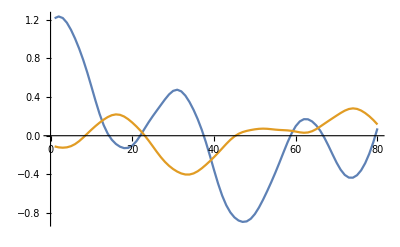

```mathematica
archetypalMeanNo = Table[Mean[Table[reducedOxyNo80[[x,y]],{x,30}]],{y,2}];
ListLinePlot[archetypalMeanNo]
```

### Time to generalize to various metrics

```mathematica
archetypal[f_]:=ListLinePlot[{Legended[f[Table[reducedOxyYes80[[x,1]],{x,30}]],"Oxy Yes"],Legended[f[Table[reducedOxyNo80[[x,1]],{x,30}]],"Oxy No"]},PlotLabel->f]
```

Test on the Mean function:

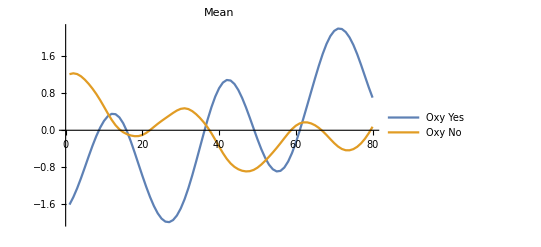

```mathematica
archetypal[Mean]
```

Generation of a list of archetypal based on standard statistical measures:

Extract::partw: Part 2 of {Directive[PointSize[0.0194444],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]]} does not exist.

Extract::partw: Part 2 of {{PointSize[0.0194444],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]}} does not exist.

Extract::partw: Part 2 of {{None,Automatic}} does not exist.

General::stop: Further output of Extract::partw will be suppressed during this calculation.

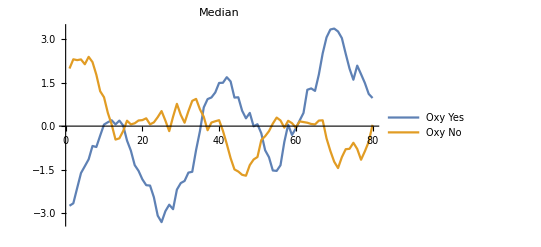
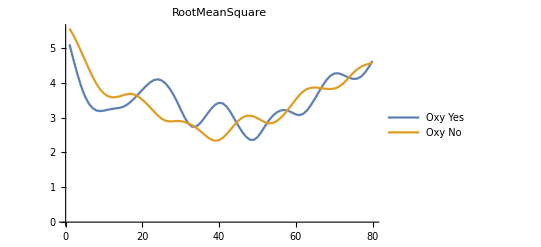
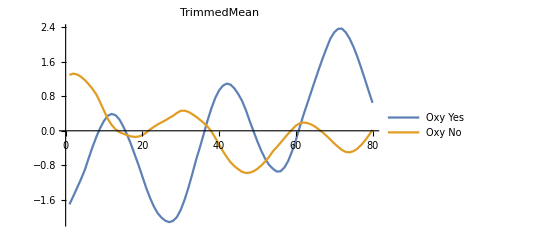
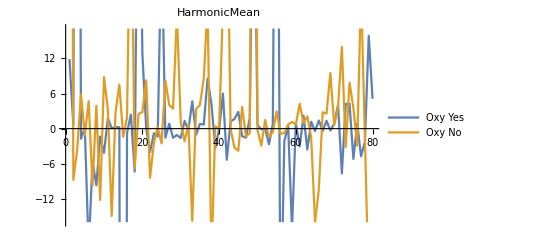
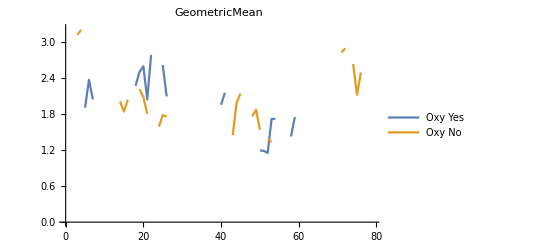
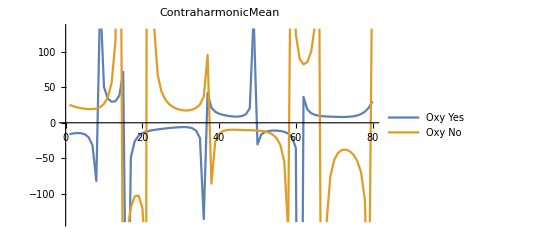
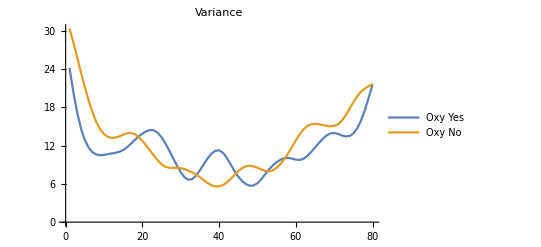
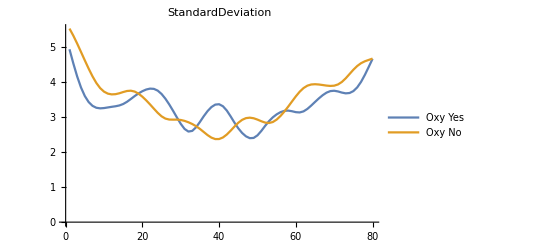
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
energy=Total@(#^2)&;
stats={Mean,Median,RootMeanSquare,TrimmedMean,HarmonicMean,GeometricMean,ContraharmonicMean,Variance,StandardDeviation,MeanDeviation,MedianDeviation,QuartileDeviation,InterquartileRange,Skewness,Kurtosis,QuartileSkewness,Entropy,energy};
Column[Style[archetypal[#],Larger]&/@stats]
```

#### Comment about the above results :

It seems like only the Mean function can give two quite different archetypals

## Experiments with DTW

```mathematica
WarpingDistance[reducedOxyYes80[[1,1]],archetypalMeanYes]
```

WarpingDistance::invarg: Expecting a real-valued numeric or boolean vector or matrix instead of {{-1.61285,-1.45139,-1.25807,-1.03949,-0.805039,-0.566394,-0.335924,-0.124856,«36»,0.874122,0.701227,0.496345,0.270944,0.0366243,-0.194463,«30»},{«19»,«49»,«30»}}.

WarpingDistance[{-3.02032,-2.18292,-1.40404,-0.699484,-0.0768349,0.444866,0.825798,1.01503,0.97392,0.698143,0.222475,-0.396134,-1.10519,-1.87333,-2.68605,-3.52528,-4.34933,-5.09052,-5.67574,-6.0565,-6.22724,-6.21992,-6.0792,-5.83441,-5.48661,-5.01861,-4.419,-3.70093,-2.90239,-2.06921,-1.23398,-0.406845,0.413908,1.2194,1.97384,2.61725,3.08636,3.34053,3.37568,3.21664,2.89467,2.42894,1.82644,1.0994,0.286347,-0.541034,-1.29443,-1.90058,-2.32679,-2.583,-2.70003,-2.69912,-2.57327,-2.29316,-1.83223,-1.19124,-0.404822,0.472935,1.39306,2.32846,3.27033,4.2074,5.106,5.90706,6.5426,6.9606,7.14167,7.09563,6.84161,6.38884,5.73421,4.87911,3.85349,2.72808,1.60194,0.570088,-0.307964,-1.01834,-1.577,-1.99973},{{-1.61285,-1.45139,-1.25807,-1.03949,-0.805039,-0.566394,-0.335924,-0.124856,0.0575081,0.203313,0.305183,0.355764,0.348564,0.280116,0.152309,-0.0268051,-0.244401,-0.485723,-0.736945,-0.986782,-1.22627,-1.44735,-1.6417,-1.80064,-1.91601,-1.98127,-1.99235,-1.94774,-1.84811,-1.69596,-1.49563,-1.2536,-0.978514,-0.680838,-0.372199,-0.0646196,0.229847,0.499011,0.730494,0.912335,1.03438,1.09016,1.07841,1.0035,0.874122,0.701227,0.496345,0.270944,0.0366243,-0.194463,-0.409676,-0.596757,-0.744972,-0.845701,-0.892412,-0.880649,-0.808518,-0.677644,-0.493981,-0.267571,-0.0106566,0.265081,0.550507,0.839058,1.12487,1.40021,1.65393,1.87232,2.04221,2.15436,2.20508,2.19564,2.13009,2.0133,1.85055,1.64892,1.41894,1.17488,0.932845,0.707515},{0.493305,0.405811,0.320935,0.241518,0.169649,0.106774,0.0541,0.0129433,-0.0153657,-0.0300697,-0.0316375,-0.0219493,-0.00388788,0.0193893,0.0450892,0.0709358,0.0947728,0.114082,0.125949,0.12758,0.117118,0.0943381,0.0608065,0.019268,-0.0273995,-0.0769896,-0.12807,-0.179476,-0.229643,-0.276272,-0.316631,-0.348255,-0.369551,-0.379894,-0.37924,-0.367528,-0.344363,-0.309293,-0.262502,-0.205333,-0.140279,-0.0704633,0.00106014,0.0717648,0.13956,0.202301,0.257377,0.301742,0.332439,0.347478,0.346517,0.330837,0.302602,0.263914,0.216235,0.160456,0.0975688,0.0294697,-0.0407833,-0.109486,-0.173175,-0.229314,-0.276398,-0.313387,-0.338871,-0.350684,-0.34641,-0.324467,-0.285107,-0.230724,-0.165257,-0.0930129,-0.0176711,0.0580006,0.131755,0.201242,0.263677,0.316204,0.356862,0.385415}}]

```mathematica
wrp[signal_List,arch_List] :=WarpingDistance[signal,arch]
```

```mathematica
distYesYes = Table[wrp[reducedOxyYes80[[x,1]],archetypalMeanYes[[1]]],{x,30}];
distYesNo = Table[wrp[reducedOxyYes80[[x,1]],archetypalMeanNo[[1]]],{x,30}];
distNoYes = Table[wrp[reducedOxyNo80[[x,1]],archetypalMeanYes[[1]]],{x,30}];
distNoNo = Table[wrp[reducedOxyNo80[[x,1]],archetypalMeanNo[[1]]],{x,30}];
```

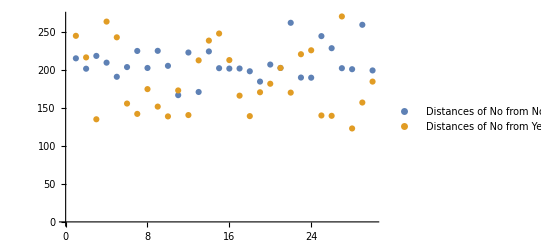

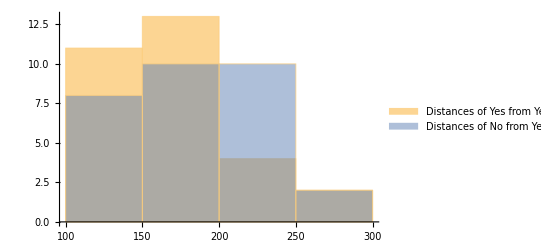

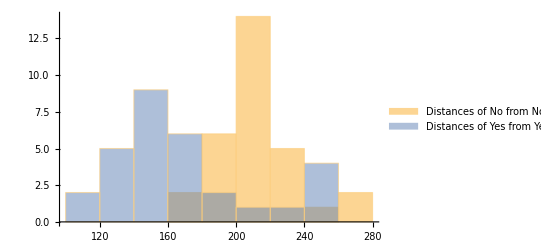

```mathematica
ListPlot[{Legended[distNoNo,"Distances of No from No"],Legended[distNoYes,"Distances of No from Yes"]}]
Histogram[{Legended[distYesYes,"Distances of Yes from Yes"],Legended[distNoYes,"Distances of No from Yes"]}]
Histogram[{Legended[distNoNo,"Distances of No from No"],Legended[distYesYes,"Distances of Yes from Yes"]}]
```

### ScatterPlot

{dYes, dNo} per ogni vec

```mathematica
distYesYesYesNo = Table[{wrp[reducedOxyYes80[[x,1]],archetypalMeanYes[[1]]],wrp[reducedOxyYes80[[x,1]],archetypalMeanNo[[1]]]},{x,30}];
```

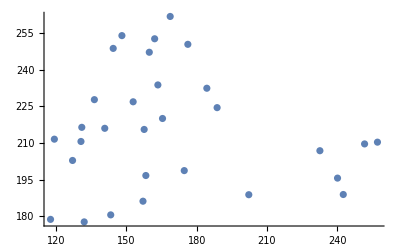

```mathematica
ListPlot[distYesYesYesNo]
```

```mathematica
distNoNoNoYes = Table[{wrp[reducedOxyNo80[[x,1]],archetypalMeanNo[[1]]],wrp[reducedOxyNo80[[x,1]],archetypalMeanYes[[1]]]},{x,30}];
```

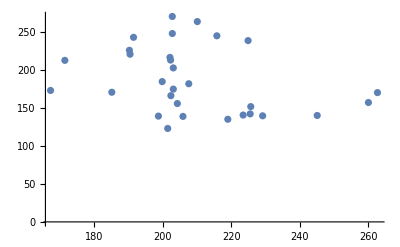

```mathematica
ListPlot[distNoNoNoYes]
```

```mathematica
30*0.3
```

9.

## Positive Drift Archetypal

```mathematica
getLineSlope[line_] := D[(Fit[line, {1,var},var]), var]
```

```mathematica
getLineSlope[reducedOxyYes80[[1,1]]]
```

0.0790202

```mathematica
positiveDriftOxyYes = Select[reducedOxyYes80[[All,1]],getLineSlope[#]>0&];
Length[positiveDriftOxyYes]
```

21

```mathematica
21/30//N
```

0.7

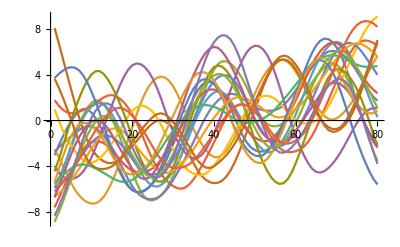

```mathematica
ListLinePlot[positiveDriftOxyYes]
```

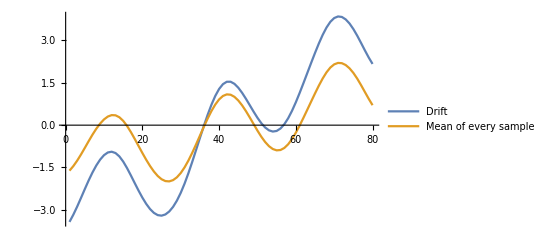

```mathematica
driftMeanArchetypalYes = Mean[positiveDriftOxyYes];
ListLinePlot[{Legended[driftMeanArchetypalYes,"Drift"],Legended[archetypalMeanYes[[1]],"Mean of every sample"]}]
```

```mathematica
positiveDriftOxyNo = Select[reducedOxyNo80[[All,1]],getLineSlope[#]<0&];
Length[positiveDriftOxyNo]
```

16

```mathematica
16/30//N
```

0.533333

```mathematica
Mean[{0.53,0.7}]
```

0.615

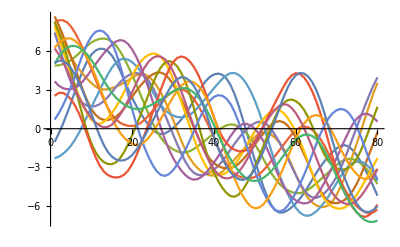

```mathematica
ListLinePlot[positiveDriftOxyNo]
```

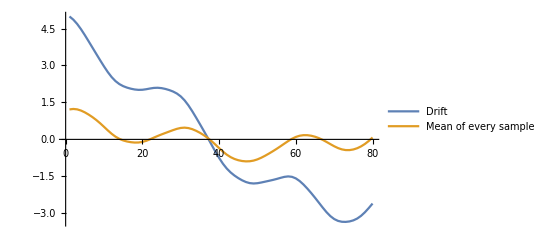

```mathematica
driftMeanArchetypalNo = Mean[positiveDriftOxyNo];
ListLinePlot[{Legended[driftMeanArchetypalNo,"Drift"],Legended[archetypalMeanNo[[1]],"Mean of every sample"]}]
```

### Plot of the 2 archetypals

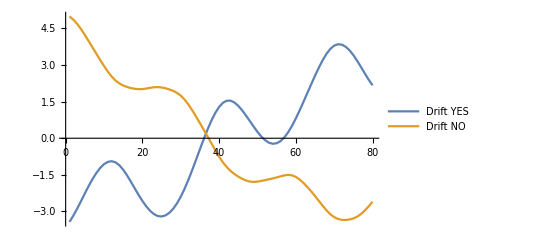

```mathematica
ListLinePlot[{Legended[driftMeanArchetypalYes,"Drift YES"],Legended[driftMeanArchetypalNo,"Drift NO"]}]
```

```mathematica
euclidDistVect[signal_List] := {EuclideanDistance[signal,driftMeanArchetypalYes],EuclideanDistance[signal,driftMeanArchetypalNo]}
```

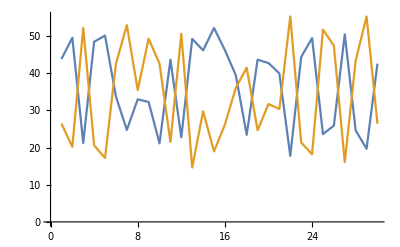

```mathematica
ListLinePlot[Transpose@Table[euclidDistVect[reducedOxyNo80[[x,1]]],{x,30}]]
```

```mathematica
dataDistArchDrift = Join[Table[euclidDistVect[reducedOxyNo80[[x,1]]]->"No",{x,30}],Table[euclidDistVect[reducedOxyYes80[[x,1]]]->"Yes",{x,30}]];
```

### Performances Assessment

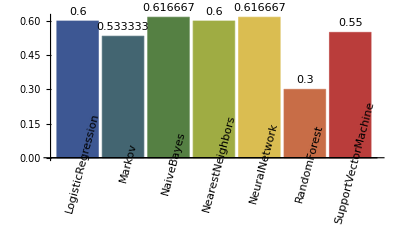

```mathematica
autoML[dataDistArchDrift]
```

Svasi a caso con la canberra

```mathematica
canbDistVect[signal_List] := {CanberraDistance[signal,driftMeanArchetypalYes],CanberraDistance[signal,driftMeanArchetypalNo]}
```

```mathematica
dataDistArchDriftCanb = Join[Table[canbDistVect[reducedOxyNo80[[x,1]]]->"No",{x,30}],Table[canbDistVect[reducedOxyYes80[[x,1]]]->"Yes",{x,30}]];
```

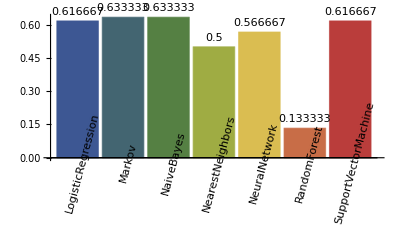

```mathematica
autoML[dataDistArchDriftCanb]
```

```mathematica
l1DistVect[signal_List] := {ManhattanDistance[signal,driftMeanArchetypalYes],ManhattanDistance[signal,driftMeanArchetypalNo]}
```

```mathematica
dataDistArchDriftL1 = Join[Table[l1DistVect[reducedOxyNo80[[x,1]]]->"No",{x,30}],Table[l1DistVect[reducedOxyYes80[[x,1]]]->"Yes",{x,30}]];
```

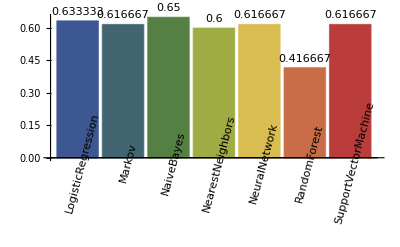

```mathematica
autoML[dataDistArchDriftL1]
```

```mathematica
corrDistVect[signal_List] := {CorrelationDistance[signal,driftMeanArchetypalYes],CorrelationDistance[signal,driftMeanArchetypalNo]}
```

```mathematica
dataDistArchDriftCorr = Join[Table[corrDistVect[reducedOxyNo80[[x,1]]]->"No",{x,30}],Table[corrDistVect[reducedOxyYes80[[x,1]]]->"Yes",{x,30}]];
```

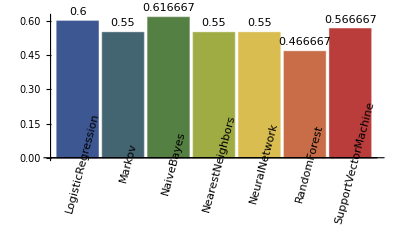

```mathematica
autoML[dataDistArchDriftCorr]
```

### With 2 components of PCA

```mathematica
dataDistArchDriftL1 = Join[Table[{l1DistVect[reducedOxyNo80[[x,1]]],l1DistVect[reducedOxyNo80[[x,2]]]}->"No",{x,30}],Table[{l1DistVect[reducedOxyYes80[[x,1]]],l1DistVect[reducedOxyYes80[[x,2]]]}->"Yes",{x,30}]];
```

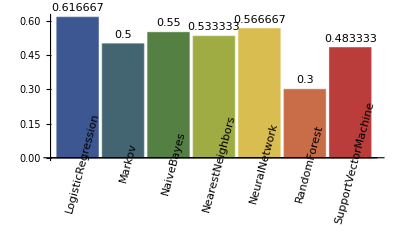

```mathematica
autoML[dataDistArchDriftL1]
```